FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

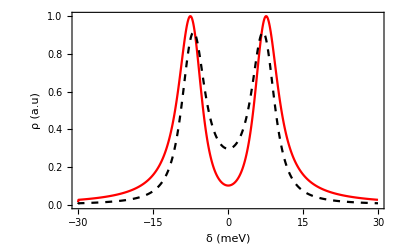

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,FontColor->Black};
SetOptions[ListPlot,BaseStyle->texStyle,Frame->True,Axes->False];
figureaQ=False;(*Change this to False to produce Figure 2 (b)*)
M=2;
{γC,γR,γV}={4,0.7,2.9};
Γ=γC+γR+γV;
g=0.5;
P0=30;
P1=P0;
P2=If[figureaQ,P0,0];
Ω0=7;
{δmin,δmax}={-30,30};
dρ[m_,n_]:=-γC ρ[m,n]+I g (J[m,n]*-J[n,m])+I Sum[Ω[m,l]ρ[n,l]*-Ω[n,l]ρ[m,l],{l,1,M}];
dR[m_]:=-γR R[m]+P[m]-I g  (J[m,m]*-J[m,m]);
dJ[m_,n_]:=-(I δ+Γ/2)J[m,n]+I g R[m](KroneckerDelta[m,n]+ρ[n,m])+I Sum[Ω[n,l]J[m,l],{l,1,M}];
eqns=Table[{dρ[m,n]==0,dJ[m,n]==0},{m,1,M},{n,1,M}];
eqns=Append[eqns,Table[dR[m]==0,{m,1,M}]];
eqns=Flatten[eqns]/.{Ω[1,1]->0,Ω[2,2]->0,Ω[1,2]->Ω0,Ω[2,1]->Ω0,P[1]->P1,P[2]->P2};
eqns=Flatten[eqns];
ρSolve[x_,{ρ11_,ρ22_,ρ12_,ρ21_,J11_,J22_,J12_,J21_,R1_,R2_}]:=Flatten[Re[{ρ[1,1],ρ[2,2],ρ[1,2],ρ[2,1],J[1,1],J[2,2],J[1,2],J[2,1],R[1],R[2]}/.FindRoot[eqns/.δ->x,{{ρ[1,1],ρ11},{ρ[2,2],ρ22},{ρ[1,2],ρ12},{ρ[2,1],ρ21},{J[1,1],J11},{J[2,2],J22},{J[1,2],J12},{J[2,1],J21},{R[1],R1},{R[2],R2}},MaxIterations->Infinity,AccuracyGoal->Infinity,PrecisionGoal->100]]];
sol={ρSolve[-40,ConstantArray[0,10]]};
Table[AppendTo[sol,ρSolve[x,sol[[-1]]]],{x,δmin,δmax,0.1}];
data=Transpose[sol][[1;;2]];
plot=ListPlot[data/Max[data],PlotRange->All,Joined->True,Frame->True,PlotStyle->{Directive[Red],Directive[Dashed,Black]},FrameLabel->{"δ (meV)","ρ (a.u)"},DataRange->{δmin,δmax}]
name=If[figureaQ,"double_cavity_1.pdf","double_cavity_2.pdf"];
Export[name,plot];
```